```mathematica
f[x_,R_]:=NIntegrate[p*Sin[p]*Exp[-I*Sqrt[p*p+1]*x],{p,0,R}];
```

```mathematica
R=100;
f[10,R]
```

-3.87854-3.39906 ⅈ

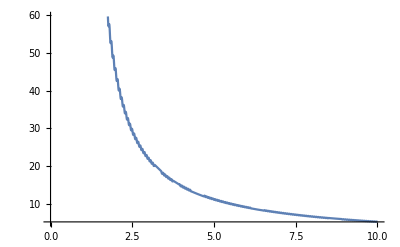

```mathematica
Plot[Abs[f[x,R]],{x,1,10},PlotRange->Automatic]
```